```mathematica
$Assumptions={t>0,d>0,l>0,v0>0};
params={mu0-> 4 Pi 10^-7,I0-> 1000,l->1,d-> 0.01,R-> 1,v0-> 100,t0->0,L-> 50/1000} // N
```

{mu0→1.25664×10^-6,I0→1000.,l→1.,d→0.01,R→1.,v0→100.,t0→0.,L→0.05}

```mathematica
(* initial calculation of needed quantities *)
B[r_]:=(mu0 I0)/(2 Pi r);
ϕ[t_]=Integrate[B[r],{r,d+v0 t,l+d+v0 t},{z,0,l}];
```

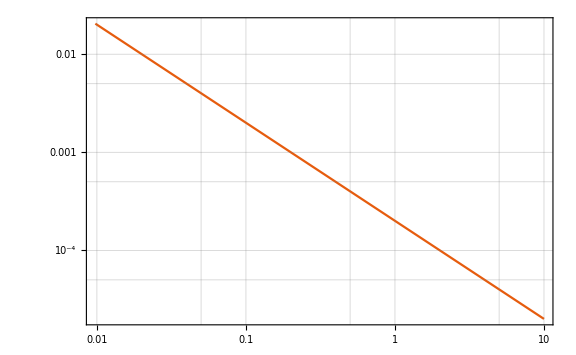
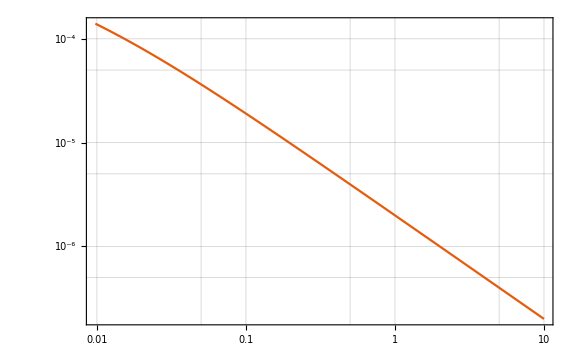

```mathematica
{LogLogPlot[B[r] /. params,{r,0,10},ImageSize->Large,PlotTheme->"Scientific",GridLines->Automatic],LogLogPlot[ϕ[t] /. params,{t,0,10},ImageSize->Large,PlotTheme->"Scientific",GridLines->Automatic]}
```

```mathematica
(* quantities needed for calculating power (only one of them) *)
proud[t_]=ϕ[t]/L;
napeti[t_]=-D[ϕ[t],t];
```

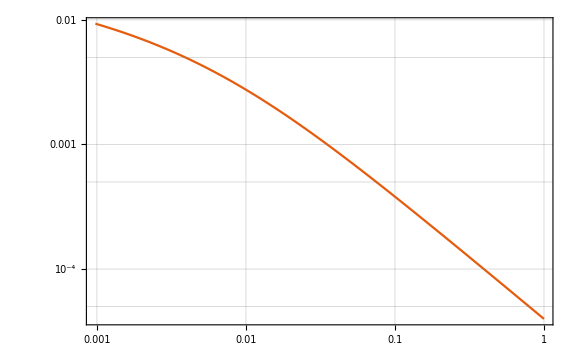
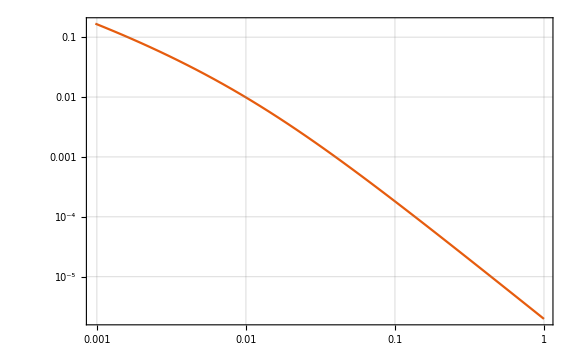

```mathematica
{LogLogPlot[proud[t]/. params,{t,0,1},ImageSize->Large,PlotTheme->"Scientific",GridLines->Automatic], LogLogPlot[napeti[t]/. params,{t,0,1},ImageSize->Large,PlotTheme->"Scientific",GridLines->Automatic]}
```

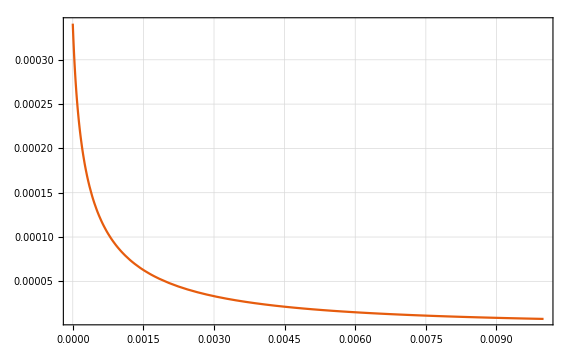

```mathematica
(* Joule heating *)
Plot[proud[t]^2 R/. params,{t,0,.01},ImageSize->Large,PlotTheme->"Scientific",GridLines->Automatic,PlotRange->All]
```

```mathematica
(* integrate power to get energy *)
NIntegrate[proud[t]^2 R /. params,{t,0,Infinity}]
```

4.74429×10^-7